```mathematica
Quit[]
```

```mathematica
Print["Gussian Filter: ", Checkbox[Dynamic[GsF]]]
```

Gussian Filter:

```mathematica
e = 1.6 10^-19;
mYb = 171 1.66 10^-27;
Ω = 2 Pi *10*10^6;
ψ=e^2/(4 mYb Ω^2);
AimedIonHeight=200*10^-6;
Vrf=200;
Altaf=0.4776;
wgnd=Sqrt[(4 AimedIonHeight^2)/(1/Altaf^2+2/Altaf)]/Altaf;
wrf=Altaf*wgnd;
zEscape=1/2Sqrt[2 wgnd wrf+wgnd^2+2(wrf+wgnd)Sqrt[2wgnd wrf+wgnd^2]];
Print["The trapping position is ",AimedIonHeight*1000000,"um"]
Print["The escaping position is ",N[zEscape]*1000000,"um"]
```

The trapping position is 200um

The escaping position is 352.899um

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory[NotebookDirectory[]];
dataRF1=Import["RF.dat","Table"];
If[FileExistsQ["dc01.dat"],
{dataDC01= Import["dc01.dat","Table"];,
dataDC02= Import["dc02.dat","Table"];,
dataDC03= Import["dc03.dat","Table"];,
dataDC04= Import["dc04.dat","Table"];,
dataDC05=Import["dc05.dat","Table"];,
dataDC06=Import["dc06.dat","Table"];,
dataDC07=Import["dc07.dat","Table"];,
dataDC08=Import["dc08.dat","Table"];,
dataDC09=Import["dc09.dat","Table"];,
dataDC10=Import["dc10.dat","Table"];,
dataDC11=Import["dc11.dat","Table"];,
dataDC12=Import["dc12.dat","Table"];}]
Print["Files loaded."]
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

Files loaded.

```mathematica
(*For[i=1,i<Length[dataRF1]+1,For[j=1,j<4,{dataRF1[[i,j]]=dataRF1[[i,j]]/1000} j++];i++]
RF1F=Table[0x y,{x,Length[dataRF1]},{y,4}];
RF1G=GaussianFilter[Table[dataRF1[[i,4]],{i,1,Length[dataRF1]}],{2,2}];
For[i=1,i<Length[RF1G]+1,i++,{RF1F[[i,3]]=dataRF1[[i,3]];
RF1F[[i,2]]=dataRF1[[i,2]];
RF1F[[i,1]]=dataRF1[[i,1]];
RF1F[[i,4]]=RF1G[[i]];}];
RF1=Interpolation[RF1F,InterpolationOrder->5];*)

(*----------------------------DEFINEING FUNCTION-----------------------------------------*)
(*ProcessData[dtf_,Gtf,ior]:=Module[{d,gsf,iod},
For[i=1,i<Length[dtf]+1,For[j=1,j<4,{dtf[[i,j]]=dtf[[i,j]]/1000} j++];
i++];
RF1F=Table[0x y,{x,Length[dtf]},{y,4}];
RF1G=GaussianFilter[Table[dtf[[i,4]],{i,1,Length[dtf]}],{2,2}];
For[i=1,i<Length[RF1G]+1,i++,{RF1F[[i,3]]=dtf[[i,3]];
RF1F[[i,2]]=dataRF1[[i,2]];
RF1F[[i,1]]=dataRF1[[i,1]];
RF1F[[i,4]]=RF1G[[i]];}];
Interpolation[RF1F,InterpolationOrder->iod]
]*)
(*----------------------------RF-----------------------------------------*)
(*--------------------------11111--------------------------------*)
For[i=1,i<Length[dataRF1]+1,For[j=1,j<4,{dataRF1[[i,j]]=dataRF1[[i,j]]/1000} j++];i++]
RF1F=Table[0x y,{x,Length[dataRF1]},{y,4}];
RF1G=GaussianFilter[Table[dataRF1[[i,4]],{i,1,Length[dataRF1]}],{2,2}];
For[i=1,i<Length[RF1G]+1,i++,{RF1F[[i,3]]=dataRF1[[i,3]];
RF1F[[i,2]]=dataRF1[[i,2]];
RF1F[[i,1]]=dataRF1[[i,1]];
RF1F[[i,4]]=RF1G[[i]];}];
RF1=Interpolation[RF1F,InterpolationOrder->5];
(*----------------------------------------------------------------------*)

(*--------------------------DC01--------------------------------*)
For[i=1,i<Length[dataDC01]+1,For[j=1,j<4,{dataDC01[[i,j]]=dataDC01[[i,j]]/1000} j++];
i++]
DC01F=Table[0x y,{x,Length[dataDC01]},{y,4}];
DC01G=GaussianFilter[Table[dataDC01[[i,4]],{i,1,Length[dataDC01]}],{2,2}];
For[i=1,i<Length[DC01G]+1,i++,{DC01F[[i,3]]=dataDC01[[i,3]];
DC01F[[i,2]]=dataDC01[[i,2]];
DC01F[[i,1]]=dataDC01[[i,1]];
DC01F[[i,4]]=DC01G[[i]];}];
DC01=Interpolation[DC01F,InterpolationOrder->5];
(*--------------------------DC02--------------------------------*)
For[i=1,i<Length[dataDC02]+1,For[j=1,j<4,{dataDC02[[i,j]]=dataDC02[[i,j]]/1000} j++];
i++]
DC02F=Table[0x y,{x,Length[dataDC02]},{y,4}];
DC02G=GaussianFilter[Table[dataDC02[[i,4]],{i,1,Length[dataDC02]}],{2,2}];
For[i=1,i<Length[DC02G]+1,i++,{DC02F[[i,3]]=dataDC02[[i,3]];
DC02F[[i,2]]=dataDC02[[i,2]];
DC02F[[i,1]]=dataDC02[[i,1]];
DC02F[[i,4]]=DC02G[[i]];}];
DC02=Interpolation[DC02F,InterpolationOrder->5];
(*--------------------------DC03--------------------------------*)
For[i=1,i<Length[dataDC03]+1,For[j=1,j<4,{dataDC03[[i,j]]=dataDC03[[i,j]]/1000} j++];
i++]
DC03F=Table[0x y,{x,Length[dataDC03]},{y,4}];
DC03G=GaussianFilter[Table[dataDC03[[i,4]],{i,1,Length[dataDC03]}],{2,2}];
For[i=1,i<Length[DC03G]+1,i++,{DC03F[[i,3]]=dataDC03[[i,3]];
DC03F[[i,2]]=dataDC03[[i,2]];
DC03F[[i,1]]=dataDC03[[i,1]];
DC03F[[i,4]]=DC03G[[i]];}];
DC03=Interpolation[DC03F,InterpolationOrder->5];
(*--------------------------DC04--------------------------------*)
For[i=1,i<Length[dataDC04]+1,For[j=1,j<4,{dataDC04[[i,j]]=dataDC04[[i,j]]/1000} j++];
i++]
DC04F=Table[0x y,{x,Length[dataDC04]},{y,4}];
DC04G=GaussianFilter[Table[dataDC04[[i,4]],{i,1,Length[dataDC04]}],{2,2}];
For[i=1,i<Length[DC04G]+1,i++,{DC04F[[i,3]]=dataDC04[[i,3]];
DC04F[[i,2]]=dataDC04[[i,2]];
DC04F[[i,1]]=dataDC04[[i,1]];
DC04F[[i,4]]=DC04G[[i]];}];
DC04=Interpolation[DC04F,InterpolationOrder->5];
(*--------------------------DC05--------------------------------*)
For[i=1,i<Length[dataDC05]+1,For[j=1,j<4,{dataDC05[[i,j]]=dataDC05[[i,j]]/1000} j++];
i++]
DC05F=Table[0x y,{x,Length[dataDC05]},{y,4}];
DC05G=GaussianFilter[Table[dataDC05[[i,4]],{i,1,Length[dataDC05]}],{2,2}];
For[i=1,i<Length[DC05G]+1,i++,{DC05F[[i,3]]=dataDC05[[i,3]];
DC05F[[i,2]]=dataDC05[[i,2]];
DC05F[[i,1]]=dataDC05[[i,1]];
DC05F[[i,4]]=DC05G[[i]];}];
DC05=Interpolation[DC05F,InterpolationOrder->5];
(*--------------------------DC06--------------------------------*)
For[i=1,i<Length[dataDC06]+1,For[j=1,j<4,{dataDC06[[i,j]]=dataDC06[[i,j]]/1000} j++];
i++]
DC06F=Table[0x y,{x,Length[dataDC06]},{y,4}];
DC06G=GaussianFilter[Table[dataDC06[[i,4]],{i,1,Length[dataDC06]}],{2,2}];
For[i=1,i<Length[DC06G]+1,i++,{DC06F[[i,3]]=dataDC06[[i,3]];
DC06F[[i,2]]=dataDC06[[i,2]];
DC06F[[i,1]]=dataDC06[[i,1]];
DC06F[[i,4]]=DC06G[[i]];}];
DC06=Interpolation[DC06F,InterpolationOrder->5];
(*--------------------------DC07--------------------------------*)
For[i=1,i<Length[dataDC07]+1,For[j=1,j<4,{dataDC07[[i,j]]=dataDC07[[i,j]]/1000} j++];
i++]
DC07F=Table[0x y,{x,Length[dataDC07]},{y,4}];
DC07G=GaussianFilter[Table[dataDC07[[i,4]],{i,1,Length[dataDC07]}],{2,2}];
For[i=1,i<Length[DC07G]+1,i++,{DC07F[[i,3]]=dataDC07[[i,3]];
DC07F[[i,2]]=dataDC07[[i,2]];
DC07F[[i,1]]=dataDC07[[i,1]];
DC07F[[i,4]]=DC07G[[i]];}];
DC07=Interpolation[DC07F,InterpolationOrder->5];
(*--------------------------DC08--------------------------------*)
For[i=1,i<Length[dataDC08]+1,For[j=1,j<4,{dataDC08[[i,j]]=dataDC08[[i,j]]/1000} j++];
i++]
DC08F=Table[0x y,{x,Length[dataDC08]},{y,4}];
DC08G=GaussianFilter[Table[dataDC08[[i,4]],{i,1,Length[dataDC08]}],{2,2}];
For[i=1,i<Length[DC08G]+1,i++,{DC08F[[i,3]]=dataDC08[[i,3]];
DC08F[[i,2]]=dataDC08[[i,2]];
DC08F[[i,1]]=dataDC08[[i,1]];
DC08F[[i,4]]=DC08G[[i]];}];
DC08=Interpolation[DC08F,InterpolationOrder->5];
(*--------------------------DC09--------------------------------*)
For[i=1,i<Length[dataDC09]+1,For[j=1,j<4,{dataDC09[[i,j]]=dataDC09[[i,j]]/1000} j++];
i++]
DC09F=Table[0x y,{x,Length[dataDC09]},{y,4}];
DC09G=GaussianFilter[Table[dataDC09[[i,4]],{i,1,Length[dataDC09]}],{2,2}];
For[i=1,i<Length[DC09G]+1,i++,{DC09F[[i,3]]=dataDC09[[i,3]];
DC09F[[i,2]]=dataDC09[[i,2]];
DC09F[[i,1]]=dataDC09[[i,1]];
DC09F[[i,4]]=DC09G[[i]];}];
DC09=Interpolation[DC09F,InterpolationOrder->5];
(*--------------------------DC10--------------------------------*)
For[i=1,i<Length[dataDC10]+1,For[j=1,j<4,{dataDC10[[i,j]]=dataDC10[[i,j]]/1000} j++];
i++]
DC10F=Table[0x y,{x,Length[dataDC10]},{y,4}];
DC10G=GaussianFilter[Table[dataDC10[[i,4]],{i,1,Length[dataDC10]}],{2,2}];
For[i=1,i<Length[DC10G]+1,i++,{DC10F[[i,3]]=dataDC10[[i,3]];
DC10F[[i,2]]=dataDC10[[i,2]];
DC10F[[i,1]]=dataDC10[[i,1]];
DC10F[[i,4]]=DC10G[[i]];}];
DC10=Interpolation[DC10F,InterpolationOrder->5];
(*--------------------------DC11--------------------------------*)
For[i=1,i<Length[dataDC11]+1,For[j=1,j<4,{dataDC11[[i,j]]=dataDC11[[i,j]]/1000} j++];
i++]
DC11F=Table[0x y,{x,Length[dataDC11]},{y,4}];
DC11G=GaussianFilter[Table[dataDC11[[i,4]],{i,1,Length[dataDC11]}],{2,2}];
For[i=1,i<Length[DC11G]+1,i++,{DC11F[[i,3]]=dataDC11[[i,3]];
DC11F[[i,2]]=dataDC11[[i,2]];
DC11F[[i,1]]=dataDC11[[i,1]];
DC11F[[i,4]]=DC11G[[i]];}];
DC11=Interpolation[DC11F,InterpolationOrder->5];
(*--------------------------DC12--------------------------------*)
For[i=1,i<Length[dataDC12]+1,For[j=1,j<4,{dataDC12[[i,j]]=dataDC12[[i,j]]/1000} j++];
i++]
DC12F=Table[0x y,{x,Length[dataDC12]},{y,4}];
DC12G=GaussianFilter[Table[dataDC12[[i,4]],{i,1,Length[dataDC12]}],{2,2}];
For[i=1,i<Length[DC12G]+1,i++,{DC12F[[i,3]]=dataDC12[[i,3]];
DC12F[[i,2]]=dataDC12[[i,2]];
DC12F[[i,1]]=dataDC12[[i,1]];
DC12F[[i,4]]=DC12G[[i]];}];
DC12=Interpolation[DC12F,InterpolationOrder->5]



Off[FindMinimum::lstol]
Off[FindMaximum::lstol]
Off[InterpolatingFunction::dmval]
```

InterpolatingFunction[{{-0.003,0.003},{-0.003,0.003},{0.,0.0007}},<>]

```mathematica
(*BOUNDARY of plot*)
xkoord1=-0.0005;
xkoord2=-xkoord1;
ykoord1=-0.0005;
ykoord2=-xkoord1;
zkoord1=0.000;
zkoord2=0.00030;
LNx=00.0005;
LNy=0.0000;
```

===RF PART===

-Graphics3D-

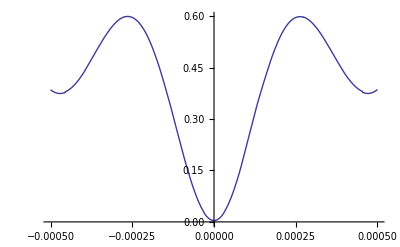

This is the potential - z

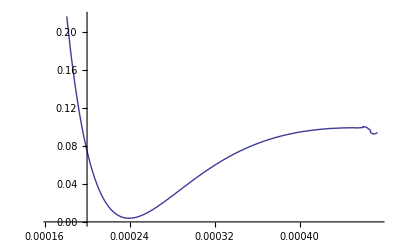

The actual ion height is 236.641 um

Escaping position is 459.083 um

The secular frequency is {898191.,829096.}

The Q parameter along x is 0.254047

Trap depth (in eV) is 0.095012

The rotation (in degree) is -0.271382.

Normalized Inhomogenous factor is 1.82578

Homogenously mapped Q parameter is 0.463833

RF driving source is 200V, 20 πMHz

```mathematica
RFbase[x_,y_,z_]=Vrf RF1[x,y,z];
RFbaseD[x_,y_,z_]=(D[RFbase[x,y,z],x])^2+(D[RFbase[x,y,z],y])^2+(D[RFbase[x,y,z],z])^2;
TotalPotentialNum[x_,y_,z_] = ψ RFbaseD[x,y,z];
DeriveTPXNum[x_,y_,z_]=D[TotalPotentialNum[x,y,z],x];
DeriveTPYNum[x_,y_,z_]=D[TotalPotentialNum[x,y,z],y];
DeriveTPZNum[x_,y_,z_]=D[TotalPotentialNum[x,y,z],z];

NumMinArr=FindMinimum[{TotalPotentialNum[LNx,LNy,z]},{z,AimedIonHeight},Method->"Newton"];
IonHeightActual=z/.NumMinArr[[2]];
xRootNum=x/.FindRoot[{DeriveTPXNum[x,y,z]==0,DeriveTPZNum[x,y,z]==0,DeriveTPYNum[x,y,z]==0},{{y,LNy},{x,LNx},{z,IonHeightActual}},AccuracyGoal->3,PrecisionGoal->3];
yRootNum=y/.FindRoot[{DeriveTPXNum[x,y,z]==0,DeriveTPZNum[x,y,z]==0,DeriveTPYNum[x,y,z]==0},{{x,LNx},{y,LNy},{z,IonHeightActual}},AccuracyGoal->3,PrecisionGoal->3];
zRootNum=z/.FindRoot[{DeriveTPXNum[x,y,z]==0,DeriveTPZNum[x,y,z]==0,DeriveTPYNum[x,y,z]==0},{{x,LNx},{y,LNy},{z,IonHeightActual}},AccuracyGoal->3,PrecisionGoal->3];
(*=========================RF PART==============================*)
Print["===RF PART==="]
HessNumMat[x_,y_,z_]=D[TotalPotentialNum[x,y,z],{{x,y,z},2}];
EigenvaluesNum=Take[Eigenvalues[HessNumMat[LNx,LNy,IonHeightActual]],2];
SecFreqNum=Sqrt[EigenvaluesNum/mYb]/(2π);
NumMaxArr=FindMaximum[{TotalPotentialNum[LNx,LNy,z],2*IonHeightActual>z>1.4IonHeightActual},{z,zEscape}];
NumMax=z/.NumMaxArr[[2]];
Plot3D[TotalPotentialNum[x,y,IonHeightActual]/e,{x,xkoord1,xkoord2},{y,ykoord1,ykoord2},ColorFunction->Hue,AspectRatio->Automatic]
Plot[TotalPotentialNum[LNx,y,IonHeightActual]/e,{y,ykoord1,ykoord2}]
Print["This is the potential - z"]
Plot[TotalPotentialNum[LNx,LNy,test]/e,{test,0.7*IonHeightActual,2*IonHeightActual}]
Print["The actual ion height is ", 1000*1000*IonHeightActual," um"]
Print["Escaping position is ",1000*1000*NumMax," um"]
Print["The secular frequency is ", SecFreqNum]
Qpara=N[2Sqrt[2]*2π*SecFreqNum[[1]]/Ω,3];
Print["The Q parameter along x is ", Qpara]
TrapDepthNum=(TotalPotentialNum[LNx,LNy,NumMax]-TotalPotentialNum[LNx,LNy,IonHeightActual])/e;
Print["Trap depth (in eV) is ",TrapDepthNum ]
EVecNum=Eigenvectors[HessNumMat[xRootNum,yRootNum,IonHeightActual]];
Print["The rotation (in degree) is ", -90+(180/π)* ArcCos[EVecNum[[1,3]]],". "]

DrevRF1Num[x_,y_,z_]=D[RFbase[x,y,z],x]+D[RFbase[x,y,z],y]+D[RFbase[x,y,z],z];

InhomoNum[x_,y_,z_]=(2e)/(mYb Ω^2)(Abs[D[DrevRF1Num[x,y,z],x]]+Abs[D[DrevRF1Num[x,y,z],y]]+Abs[D[DrevRF1Num[x,y,z],z]]);


zInhomoNum=z/.FindRoot[TotalPotentialNum[LNx,0,z]-TotalPotentialNum[LNx,0,NumMax]==0,{z,IonHeightActual-0.00005}];

InhomoThetaNum=InhomoNum[LNx,0,zInhomoNum]/InhomoNum[LNx,0,IonHeightActual];

Print["Normalized Inhomogenous factor is ",InhomoThetaNum]
Print["Homogenously mapped Q parameter is ", InhomoThetaNum*Qpara]
Print["RF driving source is " ,Vrf,"V, ", Ω*10^-6, "MHz"]

(*====RF Barrier Part====*)

(*rfBrTab=Cases[Normal@ContourPlot[TotalPotentialNum[x/1000,0 ,z/1000 ]/e,{x,rfBrXend*1000,-0.00000*1000},{z,0.00002*1000,0.00026*1000},Contours->{0.002400}],Line[pts_]->pts,Infinity];
rfBrTab[[1]]=MovingMedian[rfBrTab[[1]],6];
rfBrTab[[2]]=MovingMedian[rfBrTab[[2]],6];
rfBrTab[[2]]=Insert[rfBrTab[[2]],{-0.0,0.049},1];
rfBrTab[[1]]=Insert[rfBrTab[[1]],{-0.0,0.087},1];
ListPlot[rfBrTab,PlotRange->{Automatic,{0.04,0.12}}]
p1=Interpolation[rfBrTab[[1]]];
p2=Interpolation[rfBrTab[[2]]];
Clear[rfBrIP]
rfBrIP[x_]:=(p1[x]+p2[x])/2
(*fline=Interpolation[Table[{x,0.0883-0.01 x} ,{x,-0.007,0,0.0001}]];
rfBrIP[x_]=Piecewise[{{fline[x],-0.025<x<0},{rfBrIP[x],-0.5<x<-0.025}}];*)
tmp2=Plot[{rfBrIP[x]},{x,0,-0.5}]
Print["Contour plot"]
tmp3=ContourPlot[TotalPotentialNum[x/1000,0 ,z/1000 ]/e,{x,rfBrXend*1000,0},{z,rfBrZend*1000,rfBrZEnd*1000},Contours->120,AspectRatio->Automatic,FrameLabel->{"x (mm)","y (mm)"}, ContourLabels->Automatic,ColorFunction->Hue,PlotRange->{Automatic,{0.00004*1000,0.00015*1000}},ImageSize->Full];
Show[tmp3,tmp2]
Print["Change of rf barrier"]
Plot[TotalPotentialNum[x,0,rfBrIP[x*1000]/1000]/(e)/TrapDepthNum*100,{x,rfBrXend,0},PlotRange->{Automatic,{0,3}}]
Print["The max of barrier is ", NMaxValue[{TotalPotentialNum[x,0,rfBrIP[x*1000]/1000]/e,-0.0005<=x<-0.00005},x]/TrapDepthNum*100,"%"]*)
```

```mathematica
(*====DC Part====*)
(*Xkp=0.003;
Xkn=-0.003;
Ykp=0.003;
Ykn=-0.003;*)
Xkp=0.003;
Xkn=-0.003;
Ykp=0.003;
Ykn=-0.003;

G1=10;
G2=10;
G3=10;
G4=10;
Volt01=1;
Volt02=2 5;
Volt03=-2.5 5 ;
Volt04=1 5 ;
Volt05=0;
Volt06=0;
Volt07=2 5;
Volt08=-2 5;
Volt09=2 5;
Volt10=0;
Volt11=0;
Volt12=0;

DCPotentialNum[x_,y_,z_]=
(Volt01*DC01[x,y,z]*e)+(Volt02*DC02[x,y,z]*e)+(Volt03*DC03[x,y,z]*e)+( Volt04*DC04[x,y,z]*e)+(Volt05*DC05[x,y,z]*e)+(Volt06*DC06[x,y,z]*e)+(Volt07*DC07[x,y,z]*e)+(Volt08*DC08[x,y,z]*e)+(Volt09*DC09[x,y,z]*e)+(Volt10*DC10[x,y,z]*e)+(Volt11*DC11[x,y,z]*e)+(Volt12*DC12[x,y,z]*e);

DeriveDCXNum[x_,y_,z_]=D[DCPotentialNum[x,y,z],x];
DeriveDCYNum[x_,y_,z_]=D[DCPotentialNum[x,y,z],y];
DeriveDCZNum[x_,y_,z_]=D[DCPotentialNum[x,y,z],z];

(*Plot3D[DCPotentialNum[x,y,0]/e,{x,Xkn,Xkp},{y,Ykn,Ykp},AspectRatio->1/1,ColorFunction->Hue,PlotRange->Full]
ContourPlot[DCPotentialNum[x,0,z]/e,{x,-0.003,0.003},{z,-0.0000,0.0002},Contours->50,AspectRatio->1/1,FrameLabel->{"x (mm)","z (mm)"},FrameStyle->Medium,ContourLabels->Automatic,ColorFunction->Hue]*)
```

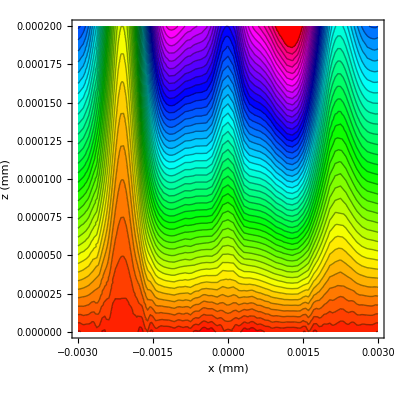

```mathematica
ContourPlot[DCPotentialNum[0,y,z]/e,{y,-0.003,0.003},{z,-0.0000,0.0002},Contours->50,AspectRatio->1/1,FrameLabel->{"x (mm)","z (mm)"},FrameStyle->Medium,ContourLabels->Automatic,ColorFunction->Hue]
```

```mathematica
(*DCx=0.0022;
DCy=0;*)
DCx=0;
DCy=-0.0022;
xRootDCNum=x/.FindRoot[{DeriveDCXNum[x,y,z]==0,DeriveDCZNum[x,y,z]==0,DeriveDCYNum[x,y,z]==0},{{y,DCy},{x,DCx},{z,IonHeightActual}},AccuracyGoal->3,PrecisionGoal->3];
yRootDCNum=y/.FindRoot[{DeriveDCXNum[x,y,z]==0,DeriveDCZNum[x,y,z]==0,DeriveDCYNum[x,y,z]==0},{{y,DCy},{x,DCx},{z,IonHeightActual}},AccuracyGoal->3,PrecisionGoal->3];
(*zRootDCNum=z/.FindRoot[{DeriveDCXNum[x,y,z]==0,DeriveDCZNum[x,y,z]==0,DeriveDCYNum[x,y,z]==0},{{y,DCy},{x,DCx},{z,IonHeightActual}},AccuracyGoal->3,PrecisionGoal->3];*)

NumMinArrDC=FindMinimum[{DCPotentialNum[xRootDCNum,yRootDCNum,z],0.8 IonHeightActual<z< 1.2IonHeightActual},{z,AimedIonHeight}];
DCNUMz=z/.NumMinArrDC[[2]];

NumMaxArrDCz=FindMaximum[{DCPotentialNum[xRootDCNum,yRootDCNum,z],2*IonHeightActual>z>0.8IonHeightActual},{z,IonHeightActual}];
NumMaxDCz=z/.NumMaxArrDCz[[2]];
SecFreqDCNumX[x_,y_,z_]=Abs[1/mYb D[DCPotentialNum[x,y,z],{x,2}]];
TrapDepthDCX=(DCPotentialNum[xRootDCNum,yRootDCNum,NumMaxDCZ]-DCPotentialNum[xRootDCNum,yRootDCNum,DCNUMz])/e;
SecFreqDCNumY[x_,y_,z_]=Abs[1/mYb D[DCPotentialNum[x,y,z],{y,2}]];
SecFreqDCNumZ[x_,y_,z_]=Abs[1/mYb D[DCPotentialNum[x,y,z],{z,2}]];
SecFreqDCx=SecFreqDCNumX[xRootDCNum,yRootDCNum,zRootDCNum]^0.5/(2 π 10^6);
SecFreqDCy=SecFreqDCNumY[xRootDCNum,yRootDCNum,zRootDCNum]^0.5/(2 π 10^6);
SecFreqDCz=SecFreqDCNumZ[xRootDCNum,yRootDCNum,zRootDCNum]^0.5/(2 π 10^6);
DCqY=2Sqrt[2] (SecFreqDCy*10^6)/Ω;
DCqZ=2Sqrt[2] (SecFreqDCz*10^6)/Ω;
Print["DC stationary position is (",xRootDCNum*10^6,",",yRootDCNum*10^6,",",DCNUMz*10^6,") um."]
Print["Secular frequency along X axis is ",SecFreqDCx,"MHz. Corresponding trap depth is ",TrapDepthDCX," eV"]
Print["Secular frequency along Y axis is ",SecFreqDCy,"MHz, while q being ", DCqY]
Print["Secular frequency along Z axis is ",SecFreqDCz,"MHz, while q being ", DCqZ]
```

DC stationary position is (-30.4301,-2135.94,274.503) um.

Secular frequency along X axis is 0.0484604MHz. Corresponding trap depth is 0.105581 eV

Secular frequency along Y axis is 0.104861MHz, while q being 0.0047204

Secular frequency along Z axis is 0.429798MHz, while q being 0.0193477